```mathematica
import[file_]:=Module[{imp,toe,data,combined,lasts},
imp=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data/"~~ToString@file];
toe=ToExpression/@StringSplit[imp];
data=Partition[toe,2];
combined=Gather[data,#1[[1]]==#2[[1]]&];
lasts={#[[1,1]],Max@#[[All,2]]}&/@combined;
{StringSplit[file,"_"][[1]],lasts}
]
```

```mathematica
SetDirectory["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data"]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data

```mathematica
data=import/@FileNames["*.txt"]
```

{{cache-lock-tt,{{1,1009},{2,2007},{3,2020},{4,2044},{5,2162},{6,2336},{7,3249},{8,4219},{9,5389},{10,9588},{11,14964},{12,20337},{13,47144},{14,56539}}},{cache-lock-tt,{{1,11},{2,2200},{3,3704},{4,3711},{5,3726},{6,3758},{7,4382},{8,5920},{9,6255},{10,7713},{11,9835},{12,29416},{13,57336},{14,57337}}},{cache-lock-tt,{{1,14},{2,2011},{3,2034},{4,5702},{5,6902},{6,7031},{7,7282},{8,7904},{9,14413},{10,16400},{11,37193},{12,56446},{13,56446}}},{cache-lock-tt,{{1,15},{2,2012},{3,2039},{4,2076},{5,12297},{6,23271},{7,23281},{8,25965},{9,57970},{13,57971}}},{cache-tt,{{1,6},{2,11},{3,22},{4,42},{5,169},{6,620},{7,1245},{8,2956},{9,5461},{10,10891},{11,13359},{12,18523},{13,46890},{14,59416}}},{cache-tt,{}},{cache-tt,{}},{cache-tt,{}},{global-smp,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,7},{7,9},{8,12},{9,18},{10,25},{11,40},{12,52},{13,123},{14,328},{15,381},{16,461},{17,890},{18,1211},{19,1842},{20,2192},{21,2952},{22,3837},{23,5046},{24,14557},{25,25149},{26,31779},{27,46417},{28,57030},{29,59755}}},{global-smp,{{1,2},{2,2},{3,2},{4,3},{5,4},{6,7},{7,8},{8,12},{9,17},{10,28},{11,40},{12,49},{13,92},{14,136},{15,287},{16,464},{17,558},{18,900},{19,1327},{20,3355},{21,3837},{22,4572},{23,6742},{24,12409},{25,13775},{26,20104},{27,34188},{28,59841},{29,59841}}},{global-smp,{{1,2},{2,2},{3,2},{4,2},{5,5},{6,6},{7,8},{8,10},{9,15},{10,23},{11,39},{12,52},{13,59},{14,181},{15,221},{16,552},{17,669},{18,949},{19,1017},{20,1614},{21,3041},{22,6807},{23,9980},{24,11735},{25,16146},{26,21171},{27,30066},{28,32394},{29,56465},{30,59842}}},{global-smp,{{1,2},{2,2},{3,2},{4,3},{5,4},{6,6},{7,7},{8,8},{9,10},{10,23},{11,47},{12,104},{13,168},{14,217},{15,381},{16,601},{17,726},{18,1337},{19,1535},{20,1731},{21,2055},{22,3646},{23,10194},{24,17701},{25,19374},{26,39225},{27,59841},{28,59841}}},{irreversible-tt,{{1,11},{2,19},{3,53},{4,107},{5,423},{6,1243},{7,2715},{8,4199},{9,12491},{10,20358},{11,59427}}},{irreversible-tt,{}},{irreversible-tt,{}},{irreversible-tt,{}},{naive-tt,{{1,11},{2,20},{3,50},{4,99},{5,562},{6,841},{7,1331},{8,3839},{9,16334},{10,22169},{11,55393},{12,59331}}},{naive-tt,{}},{naive-tt,{}},{naive-tt,{}},{stockfish-master,{{1,2},{2,2},{3,2},{4,2},{5,3},{6,6},{7,7},{8,9},{9,14},{10,22},{11,35},{12,47},{13,158},{14,281},{15,446},{16,670},{17,1105},{18,1717},{19,2529},{20,2865},{21,3690},{22,6801},{23,12980},{24,15714},{25,20404},{26,29578},{27,38600},{28,48923},{29,59985}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,5},{7,9},{8,11},{9,15},{10,24},{11,56},{12,68},{13,113},{14,187},{15,272},{16,413},{17,527},{18,963},{19,1722},{20,2039},{21,3104},{22,4122},{23,6083},{24,11602},{25,14891},{26,33934},{27,51182},{28,59984}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,2},{5,5},{6,6},{7,8},{8,11},{9,17},{10,22},{11,30},{12,52},{13,116},{14,185},{15,257},{16,453},{17,567},{18,1342},{19,1600},{20,2387},{21,3675},{22,5507},{23,7807},{24,9238},{25,13347},{26,15600},{27,22623},{28,27692},{29,41126},{30,59984}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,3},{5,4},{6,6},{7,7},{8,9},{9,11},{10,17},{11,27},{12,52},{13,83},{14,231},{15,355},{16,538},{17,599},{18,774},{19,989},{20,1611},{21,3490},{22,4987},{23,5814},{24,7916},{25,10207},{26,16984},{27,19483},{28,31846},{29,47153},{30,59984}}}}

```mathematica
medians=Gather[data,#1[[1]]==#2[[1]]&]//{#[[1,1]],Sequence@@#&/@#[[All,2,All]]}&/@#&//{#[[1]],{#[[1,1]],Median@#[[All,2]]}&/@Gather[#[[2]],#[[1]]==#2[[1]]&]}&/@#&
```

{{cache-lock-tt,{{1,29/2},{2,4023/2},{3,4073/2},{4,5787/2},{5,5314},{6,10789/2},{7,5832},{8,6912},{9,10334},{10,9588},{11,14964},{12,29416},{13,56891},{14,56938}}},{cache-tt,{{1,6},{2,11},{3,22},{4,42},{5,169},{6,620},{7,1245},{8,2956},{9,5461},{10,10891},{11,13359},{12,18523},{13,46890},{14,59416}}},{global-smp,{{1,2},{2,2},{3,2},{4,5/2},{5,4},{6,13/2},{7,8},{8,11},{9,16},{10,24},{11,40},{12,52},{13,215/2},{14,199},{15,334},{16,508},{17,1395/2},{18,1080},{19,1431},{20,3923/2},{21,5993/2},{22,8409/2},{23,8361},{24,13483},{25,17760},{26,26475},{27,80605/2},{28,116871/2},{29,59755},{30,59842}}},{irreversible-tt,{{1,11},{2,19},{3,53},{4,107},{5,423},{6,1243},{7,2715},{8,4199},{9,12491},{10,20358},{11,59427}}},{naive-tt,{{1,11},{2,20},{3,50},{4,99},{5,562},{6,841},{7,1331},{8,3839},{9,16334},{10,22169},{11,55393},{12,59331}}},{stockfish-master,{{1,2},{2,2},{3,2},{4,2},{5,4},{6,6},{7,15/2},{8,10},{9,29/2},{10,22},{11,65/2},{12,52},{13,229/2},{14,209},{15,627/2},{16,991/2},{17,583},{18,2305/2},{19,1661},{20,2213},{21,7165/2},{22,5247},{23,6945},{24,10420},{25,14119},{26,23281},{27,61223/2},{28,80769/2},{29,47153},{30,59984}}}}

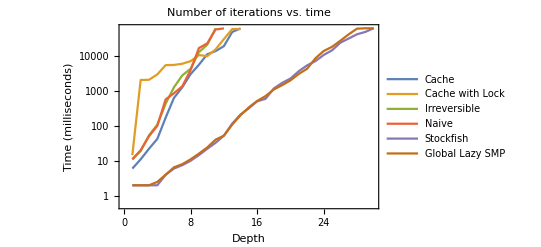

```mathematica
ttdGraph=Module[{d,cache,cachelock,globallazysmp,irreversible,naive,stockfish,legends,labels,lp,joined},
d=medians;
cache=Select[d,#[[1]]=="cache-tt"&][[1,2]];
cachelock=Select[d,#[[1]]=="cache-lock-tt"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible-tt"&][[1,2]];
naive=Select[d,#[[1]]=="naive-tt"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish-master"&][[1,2]];
globallazysmp=Select[d,#[[1]]=="global-smp"&][[1,2]];

legends={"Cache","Cache with Lock","Irreversible","Naive","Stockfish","Global Lazy SMP"};
labels={"Depth","Time (milliseconds)"};
lp=ListLogPlot[{cache,cachelock,irreversible,naive,stockfish,globallazysmp},PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[{cache,cachelock,irreversible,naive,stockfish,globallazysmp},PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[{cache,cachelock,irreversible,naive,stockfish,globallazysmp},PlotLegends->legends,PlotLabel->"Number of iterations vs. time",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

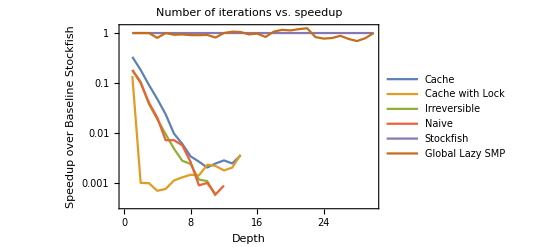

```mathematica
ttdSpeedupGraph=Module[{d,cache,cachelock,globallazysmp,irreversible,naive,stockfish,legends,labels,lp,joined,tS,speedup,alldata},
d=medians;
cache=Select[d,#[[1]]=="cache-tt"&][[1,2]];
cachelock=Select[d,#[[1]]=="cache-lock-tt"&][[1,2]];
irreversible=Select[d,#[[1]]=="irreversible-tt"&][[1,2]];
naive=Select[d,#[[1]]=="naive-tt"&][[1,2]];
stockfish=Select[d,#[[1]]=="stockfish-master"&][[1,2]];
globallazysmp=Select[d,#[[1]]=="global-smp"&][[1,2]];
tS=stockfish[[All,2]];
speedup[data_]:=MapThread[{#[[1]],#2/#[[2]]}&,{data,tS[[;;Length@data]]}];

legends={"Cache","Cache with Lock","Irreversible","Naive","Stockfish","Global Lazy SMP"};
labels={"Depth","Speedup over Baseline Stockfish"};
alldata={cache,cachelock,irreversible,naive,stockfish,globallazysmp};
lp=ListLogPlot[speedup/@alldata,PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[1]];
joined=ListLogPlot[alldata,PlotLegends->legends,FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True][[2]];
ListLogPlot[speedup/@alldata,PlotLegends->legends,PlotLabel->"Number of iterations vs. speedup",FrameLabel->labels,Frame->{{True,False},{True,False}},Joined->True]
]
```

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/timetodepth.png",ttdGraph]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/timetodepth.png

```mathematica
Export["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/speedup.png",ttdSpeedupGraph]
```

/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/plots/speedup.png

```mathematica
?Gather
```

Gather[list] gathers the elements of list into sublists of identical elements.
Gather[list,test] applies test to pairs of elements to determine if they should be considered identical.

```mathematica
importTT=Module[{imp,toe,sp,toexpression,addthreadsmins,parse,joined},
imp=Import["/Users/hasslerthurston/Academia/UR/Courses/CSC/CSC258/distributed-stockfish/data/STDOUT4"];
toe=StringSplit[imp,"\n"];
sp=Split[toe,((StringStartsQ[#,"threads"])&&(!StringStartsQ[#2,"threads"]))||((!StringStartsQ[#,"threads"])&&(!StringStartsQ[#2,"threads"]))&];
parse[toprow_]:=ToExpression/@StringSplit[toprow,{" ",","}][[3;;;;4]];
toexpression={parse@#[[1]],Sequence@@ToExpression/@StringSplit/@#[[2;;]]}&/@sp;
joined=Table[{Sequence@@#[[1]],Sequence@@#[[i]]},{i,2,Length@#}]&/@toexpression;
Median/@joined
]
```

{{2.,1.,5.,0.0396719,0.135449,0.00298563},{2.,2.,5.,0.0792436,0.253236,0.0405833},{2.,3.,5.,0.131413,0.396968,0.0165414},{2.,5.,5.,0.196438,0.540191,0.0562721},{2.,10.,5.,0.377404,0.824106,0.0644945},{2.,15.,5.,0.517467,0.9296,0.0904216},{2.,30.,5.,0.769484,0.996117,2.58925},{3.,1.,5.,0.0460015,0.154497,0.0134927},{3.,2.,5.,0.0934759,0.282068,0.00814249},{3.,3.,5.,0.132243,0.388722,0.0188472},{3.,5.,5.,0.206077,0.545473,0.01725},{3.,10.,5.,0.362137,0.801777,0.0594127},{3.,15.,5.,0.478242,0.898384,0.0403004},{3.,30.,5.,0.747018,0.993855,0.0589786},{4.,1.,5.,0.0539991,0.159766,0.0146044},{4.,2.,5.,0.101239,0.296327,0.00743312},{4.,3.,5.,0.154311,0.424804,0.020825},{4.,5.,5.,0.237411,0.590791,0.0223343},{4.,10.,5.,0.43232,0.852999,0.0880214},{4.,15.,5.,0.566008,0.950498,0.165378},{4.,30.,5.,0.797827,0.997445,0.0714187},{6.,1.,5.,0.0523085,0.150687,0.00945573},{6.,2.,5.,0.109872,0.294101,0.0283131},{6.,3.,5.,0.165528,0.431082,0.0209728},{6.,5.,5.,0.260985,0.617161,0.0233128},{6.,10.,5.,0.435077,0.857665,0.0578583},{6.,15.,5.,0.564477,0.951874,0.0664234},{6.,30.,5.,0.805336,0.998004,0.142124},{8.,1.,5.,0.0574794,0.158086,0.00696096},{8.,2.,5.,0.111489,0.300995,0.0128508},{8.,3.,5.,0.166134,0.424725,0.0245091},{8.,5.,5.,0.266205,0.623931,0.0329361},{8.,10.,5.,0.442511,0.863403,0.149713},{8.,15.,5.,0.574658,0.953584,0.115134},{8.,30.,5.,0.799025,0.997945,0.0954112},{12.,1.,4.,0.0603462,0.158423,0.00757878},{12.,2.,4.,0.118748,0.300305,0.0272294},{12.,3.,4.,0.167766,0.425849,0.0179479},{12.,5.,4.,0.258876,0.612872,0.0432553},{12.,10.,4.,0.429538,0.856315,0.0498563},{12.,15.,4.,0.552968,0.947096,0.0446603},{12.,30.,4.,0.781546,0.997205,0.126641}}

```mathematica
colorData=SplitBy[importTT,First]
```

{{{2.,1.,5.,0.0396719,0.135449,0.00298563},{2.,2.,5.,0.0792436,0.253236,0.0405833},{2.,3.,5.,0.131413,0.396968,0.0165414},{2.,5.,5.,0.196438,0.540191,0.0562721},{2.,10.,5.,0.377404,0.824106,0.0644945},{2.,15.,5.,0.517467,0.9296,0.0904216},{2.,30.,5.,0.769484,0.996117,2.58925}},{{3.,1.,5.,0.0460015,0.154497,0.0134927},{3.,2.,5.,0.0934759,0.282068,0.00814249},{3.,3.,5.,0.132243,0.388722,0.0188472},{3.,5.,5.,0.206077,0.545473,0.01725},{3.,10.,5.,0.362137,0.801777,0.0594127},{3.,15.,5.,0.478242,0.898384,0.0403004},{3.,30.,5.,0.747018,0.993855,0.0589786}},{{4.,1.,5.,0.0539991,0.159766,0.0146044},{4.,2.,5.,0.101239,0.296327,0.00743312},{4.,3.,5.,0.154311,0.424804,0.020825},{4.,5.,5.,0.237411,0.590791,0.0223343},{4.,10.,5.,0.43232,0.852999,0.0880214},{4.,15.,5.,0.566008,0.950498,0.165378},{4.,30.,5.,0.797827,0.997445,0.0714187}},{{6.,1.,5.,0.0523085,0.150687,0.00945573},{6.,2.,5.,0.109872,0.294101,0.0283131},{6.,3.,5.,0.165528,0.431082,0.0209728},{6.,5.,5.,0.260985,0.617161,0.0233128},{6.,10.,5.,0.435077,0.857665,0.0578583},{6.,15.,5.,0.564477,0.951874,0.0664234},{6.,30.,5.,0.805336,0.998004,0.142124}},{{8.,1.,5.,0.0574794,0.158086,0.00696096},{8.,2.,5.,0.111489,0.300995,0.0128508},{8.,3.,5.,0.166134,0.424725,0.0245091},{8.,5.,5.,0.266205,0.623931,0.0329361},{8.,10.,5.,0.442511,0.863403,0.149713},{8.,15.,5.,0.574658,0.953584,0.115134},{8.,30.,5.,0.799025,0.997945,0.0954112}},{{12.,1.,4.,0.0603462,0.158423,0.00757878},{12.,2.,4.,0.118748,0.300305,0.0272294},{12.,3.,4.,0.167766,0.425849,0.0179479},{12.,5.,4.,0.258876,0.612872,0.0432553},{12.,10.,4.,0.429538,0.856315,0.0498563},{12.,15.,4.,0.552968,0.947096,0.0446603},{12.,30.,4.,0.781546,0.997205,0.126641}}}

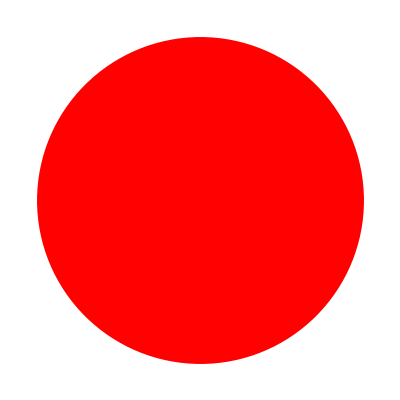
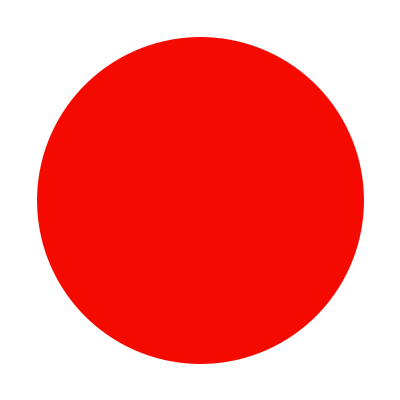
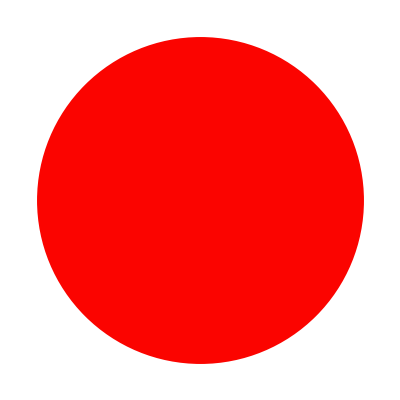
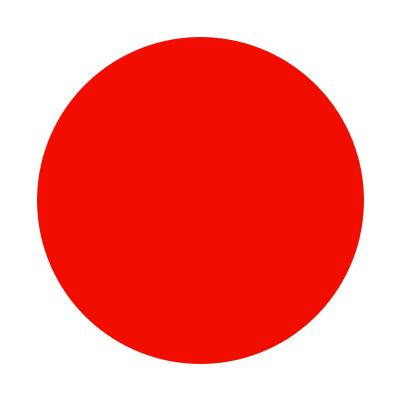
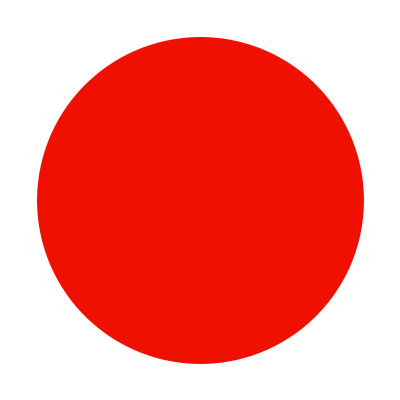
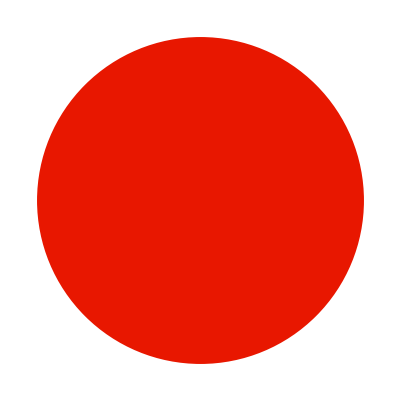
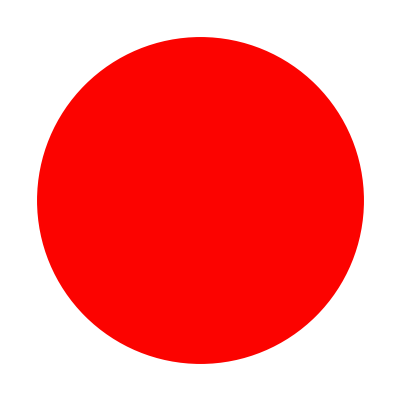
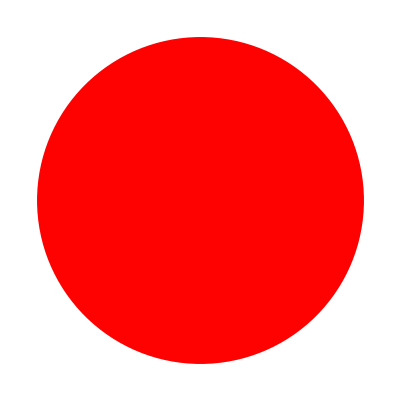
2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | 
3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
12 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | 1 | 2 | 3 | 5 | 10 | 15 | 30Number of minutesNumber of threadsPercentage of accesses to Transposition Table which are Reads

```mathematica
writePercentageGraph=Module[{color,gr,gr2,gr3,realGrid,l},
color[num_]:=Module[{dat,percent,red,green},
dat=colorData[[All,All,-1]];
dat=Select[#,#≤1&]&/@dat;
percent=(num-Min@Flatten@dat)/(Max@Flatten@dat-Min@Flatten@dat);
percent=num;
RGBColor[1-percent,percent,0]
];
gr=Graphics[{color[#],Disk[{0,0},#]}]&/@#&/@colorData[[All,All,-1]];gr2=MapThread[Prepend[#,#2]&,{gr,{2,3,4,6,8,12}}];
gr3=Append[gr2,{"",1,2,3,5,10,15,30}];
gr3[[1]][[8]]="";
realGrid=Grid[gr3,Frame->{{None,{True}},{{True},None}},ItemSize->{4,4}];l=Labeled[realGrid,{"Number of minutes","Number of threads","Percentage of accesses to Transposition Table which are Reads",""},All,RotateLabel->True]
]
```

```mathematica
cd={#[[1,1]],Median@#[[All,-3;;]]}&/@colorData
```

{{2.,{0.196438,0.540191,0.0562721}},{3.,{0.206077,0.545473,0.0188472}},{4.,{0.237411,0.590791,0.0223343}},{6.,{0.260985,0.617161,0.0283131}},{8.,{0.266205,0.623931,0.0329361}},{12.,{0.258876,0.612872,0.0432553}}}

```mathematica
cd[[All,1]]
```

{2.,3.,4.,6.,8.,12.}

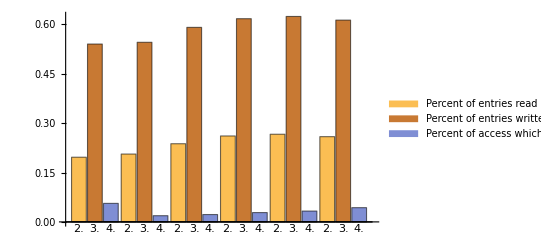

```mathematica
BarChart[cd[[All,2]],ChartLabels->cd[[All,1]],ChartLegends->{"Percent of entries read","Percent of entries written to","Percent of access which were reads"}]
```